```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<"HeterogeneousTemplate.wl";

GenerateMarkovTemplates[  MarkovProc_, NumTemplates_, LenTemplates_ ] :=
	(RandomFunction[MarkovProc,{#,LenTemplates}][[2]][[1]][[1]])&/@ConstantArray[1,NumTemplates];

RandomMarkovError[  Alphabet_,ProbVec_, LenTemplates_ ,gpo_,EnergyMatrix_,KineticMatrix_ ] :=  Module[ {inputtemplate,ErrorProbs},
	inputtemplate = RandomChoice[ ProbVec->Range[Alphabet],LenTemplates];
	ErrorProbs=GetAverageEntropyRate[GetTransferMatrixList[gpo,
		EnergyMatrix,KineticMatrix,inputtemplate]];
	Return[ErrorProbs];
 ]
```

```mathematica
For[ gpo = -Log[2], gpo < 0.04, gpo = gpo+0.05,
	PreDomain =  Range[0,1,0.05];
	ErrorData= {};
	Domain = {1-#,#} &/@PreDomain;
	
	For [ x = 0.0,x<=6.1,x = x+1.0,
		EnergyMatrix =  {{6.0,x},{0.0,6.0}};
		KineticMatrix =  {{0.0,0.0},{0.0,0.0}};
		MeanErrors =RandomMarkovError[  2,#,10000,gpo,EnergyMatrix,KineticMatrix]&/@Domain;
		ErrorData =Append[ErrorData,Transpose@{PreDomain,MeanErrors}];
	];
	Save[StringJoin[{"Entrop",ToString[Round[gpo,0.01]]}],ErrorData];
	Print[gpo]
]
```

-Log[2]

-0.643147

-0.593147

-0.543147

-0.493147

-0.443147

-0.393147

-0.343147

-0.293147

-0.243147

-0.193147

-0.143147

-0.0931472

-0.0431472

0.00685282

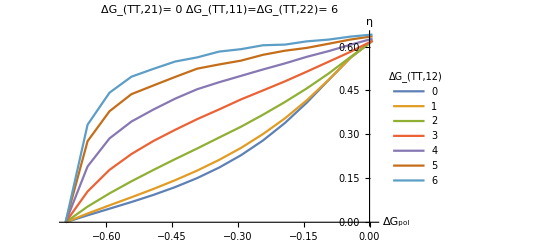

```mathematica
DataVec = {};
For[ gpo = -Log[2], gpo < 0.04, gpo = gpo+0.05,
	ErrorData = Get[StringJoin[{"Entrop",ToString[Round[gpo,0.01]]}]];
	DataVec = Append[DataVec, If [ gpo > -Log[2],
		{gpo,Max[(Log[2]-#[[All,2]])/(Log[2]+gpo) ]}&/@ ErrorData,
		{gpo,Max[(Log[2]-#[[All,2]])/(Log[2]+gpo+0.0001)]}&/@ ErrorData]];	
]
transed = Transpose[DataVec];
Save["EntropyData",transed]
 mu={0,1,2,3,4,5,6};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","TT,12"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListLinePlot[Transpose[DataVec],AxesLabel->{Subscript["ΔG","pol"],"η"},
		PlotLegends->Placed[pl,Right],PlotLabel->Row[{Subscript["ΔG","TT,21"],"= 0    ", Subscript["ΔG","TT,11"],"=",
		Subscript["ΔG","TT,22"],"= 6    "}]];
Show[{p1}]
```

```mathematica
DataVec = {};
For[ gpo = -Log[2]+0.05, gpo < 0.04, gpo = gpo+0.05,
	ErrorData = Get[StringJoin[{"Entrop",ToString[Round[gpo,0.01]]}]];
	DataVec = Append[DataVec,{gpo,-Max[#[[All,2]]-Log[2] ]}&/@ ErrorData];	
]

 mu={0,1,2,3,4,5,6};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","TT,12"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListLinePlot[Transpose[DataVec],AxesLabel->{Subscript["ΔG","pol"],"H"},
		PlotLegends->Placed[pl,Right],PlotLabel->Row[{Subscript["ΔG","TT,21"],"= 0    ", Subscript["ΔG","TT,11"],"=",
		Subscript["ΔG","TT,22"],"= 6    "}]];
p2 = Graphics[{Thick,Dashed,Line[{ErrorData[[7]][[1]],ErrorData[[7]][[-1]]}]}];
p3 = Graphics[{Thick,Dashed,Line[{ErrorData[[4]][[1]],ErrorData[[4]][[-1]]}]}];
Show[{p1,p2,p3}]
```

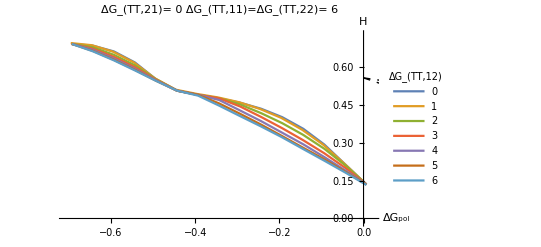

```mathematica
(*Having Observed these interesting trends, we now attempt to explain it.*)

(*Investigate the most extreme example of an archetypal case: gpo = -0.24.., GTT1,2 = 6*)
gpo = -Log[2]+0.01;
PreDomain =  Range[0,1,0.05];
ErrorData= {};
Domain = {1-#,#} &/@PreDomain;
	
	For [ x = 0.0,x<=6.1,x = x+1.0,
		EnergyMatrix =  {{6.0,x},{0.0,6.0}};
		KineticMatrix =  {{0.0,0.0},{0.0,0.0}};
		MeanErrors =RandomMarkovError[  2,#,10000,gpo,EnergyMatrix,KineticMatrix]&/@Domain;
		ErrorData =Append[ErrorData,Transpose@{PreDomain,MeanErrors}];
	];
	Save[StringJoin[{"Entrop",ToString[Round[-Log[2],0.01]]}],ErrorData];
	Print[gpo]
```

$Aborted

-0.683147

```mathematica
(*We see that the peak is at about 40% Monomer 2 *)

(*Let's first re run the entropy code as a sanity check*)
```

```mathematica
EnergyMatrix =  {{6.0,6.0},{0.0,6.0}};
KineticMatrix =  EnergyMatrix;
gpo = -0.24;

inputtemplate = RandomChoice[ {0.6,0.4}->{1,2},10000];
(Log[2]-GetAverageEntropyRate[GetTransferMatrixList[gpo,
		EnergyMatrix,KineticMatrix,inputtemplate]])/(Log[2]+gpo)
(Log[2]-GetAverageEntropyRate[GetTransferMatrixList[gpo,
		EnergyMatrix,KineticMatrix,ConstantArray[1,10000]]])/(Log[2]+gpo)
```

0.730651

0.572585

```mathematica
EnergyMatrix =  {{6.0,6.0},{0.0,6.0}};
KineticMatrix =  EnergyMatrix;
gpo = -0.24;

inputtemplate = RandomChoice[ {0.6,0.4}->{1,2},100]
GetEntropyRate[GetTransferMatrixList[gpo,
		EnergyMatrix,KineticMatrix,inputtemplate]]
GetEntropyRate[GetTransferMatrixList[gpo,
		EnergyMatrix,KineticMatrix,ConstantArray[1,100]]]
```

{2,2,1,1,1,2,1,1,2,1,2,1,2,1,1,1,2,1,2,1,1,1,2,2,2,1,1,1,2,1,2,2,2,1,1,1,1,1,2,1,2,1,2,2,1,1,1,1,2,1,1,2,1,1,2,1,1,1,2,1,1,2,1,1,1,2,1,2,2,2,1,1,1,2,2,2,2,1,2,2,1,1,2,1,2,2,2,1,1,1,1,1,1,1,1,2,2,1,2,1}

{0.693147,0.693147,0.138297,0.11217,0.118924,0.693147,0.105632,0.108646,0.693147,0.122197,0.693147,0.136488,0.693147,0.120721,0.0971818,0.101897,0.693147,0.113382,0.693147,0.0976761,0.0775414,0.0797083,0.693147,0.693147,0.693147,0.124939,0.100778,0.105974,0.693147,0.118665,0.693147,0.693147,0.693147,0.195137,0.160724,0.13779,0.115898,0.123042,0.693147,0.14086,0.693147,0.159608,0.693147,0.693147,0.19728,0.162554,0.139506,0.149973,0.693147,0.138577,0.143681,0.693147,0.131963,0.136688,0.693147,0.124499,0.100403,0.105548,0.693147,0.0917348,0.0937184,0.693147,0.0796025,0.0621439,0.0623756,0.693147,0.0622946,0.693147,0.693147,0.693147,0.0889934,0.0701441,0.0713772,0.693147,0.693147,0.693147,0.693147,0.18984,0.693147,0.693147,0.236852,0.244957,0.693147,0.306498,0.693147,0.693147,0.693147,0.468296,0.382446,0.389102,0.378689,0.369374,0.358023,0.343052,0.392803,0.693147,0.693147,0.592103,0.693147,0.0173114}

{0.0276695,0.518946,0.415778,0.437509,0.432932,0.433896,0.433693,0.433736,0.433727,0.433729,0.433728,0.433728,0.433728,0.433728,0.433728,0.433728,0.433728,0.433729,0.433729,0.433729,0.433729,0.433729,0.433729,0.433729,0.433729,0.433729,0.43373,0.43373,0.43373,0.43373,0.433731,0.433731,0.433732,0.433732,0.433733,0.433734,0.433734,0.433735,0.433736,0.433738,0.433739,0.433741,0.433743,0.433745,0.433748,0.43375,0.433754,0.433758,0.433762,0.433767,0.433773,0.43378,0.433788,0.433797,0.433808,0.43382,0.433834,0.43385,0.433869,0.43389,0.433915,0.433943,0.433975,0.434013,0.434056,0.434106,0.434163,0.434229,0.434305,0.434392,0.434493,0.434608,0.434741,0.434894,0.43507,0.435272,0.435504,0.43577,0.436076,0.436427,0.43683,0.437291,0.437819,0.438422,0.439111,0.439898,0.440793,0.441811,0.442965,0.44427,0.445742,0.447396,0.449247,0.451305,0.453593,0.456021,0.459344,0.457704,0.491083,0.0173114}

```mathematica
Log[2]-0.0001
```

0.693047

```mathematica
Transpose[DataVec]
```

{}